Predicting the electron Invariant mass from the CERN dielectron collision data 
by Shivam Sawarn
Hindu College, Delhi University

Abstract: The project aims at exploring various features of the dielectron collision using rigorous data analysis tools. The dataset consisting 100,000 dielectron events in the invariant mass range 2-110 GeV is also used to train the neural network. The neural network is used on test dataset to predict the invariant mass of the electron.

## Introduction

Since the 1970s, particle physicists have described the fundamental structure of matter using an elegant series of equations called the Standard Model. The model describes how everything that we observe in the universe is made from a few basic blocks called fundamental particles, governed by four forces. Physicists use the world’s most powerful particle accelerators and detectors to test the predictions and limits of the Standard Model. Over the years it has explained many experimental results and precisely predicted a range of phenomena, such that today it is considered a well-tested physics theory. Scientists believe that we may see a unification of forces in the high energy spectrum which is why the collision at high energies are of interest.
There are four fundamental forces at work in the universe: the strong force, the weak force, the electromagnetic force, and the gravitational force. They work over different ranges and have different strengths. Despite its name, the weak force is much stronger than gravity but it is indeed the weakest of the other three. Three of the fundamental forces result from the exchange of force-carrier particles, which belong to a broader group called “bosons”.  Each fundamental force has its own corresponding boson – the strong force is carried by the “gluon”, the electromagnetic force is carried by the “photon”, and the “W and Z bosons” are responsible for the weak force.

#### Z- Boson

Discovered in 1983 by physicists at the Super Proton Synchrotron at CERN, The Z boson is a neutral elementary particle which along with its electrically charged cousin, the W - carries the weak force .
   The weak force is essentially as strong as the electromagnetic force, but it appears weak because its influence is limited by the large mass of the Z and W bosons . Their mass limits the range of the weak force to about 10 - 18 metres, and it vanishes altogether beyond the radius of a single proton .
  Physicists working with the Gargamelle bubble chamber experiment at CERN presented the first convincing evidence to support this idea in 1973. Neutrinos are particles that interact only via the weak interaction, and when the physicists shot neutrinos through the bubble chamber they were able to detect evidence of the weak neutral current, and hence indirect evidence for the Z boson .
  Although more time and analysis is needed to determine if this is the particle predicted by the Standard Model, the discovery of the elusive Z bosons set the stage for this important development . The 2013 Nobel Prize in Physics has been awarded to two of the theorists who formulated the Higgs mechanism, which gives mass to fundamental particles like electrons.

#### Theory

Particle theorists seldom include the c’s and ℏ’s in their formulas. One is just supposed to fit them at the end, to make the dimensions come out right i.e. one may assume  c=ℏ=1
Location of a particle is described by a 4-component coordinate vector : x^μ=(t,x,y,z)
Particle kinematics is described by 4-component vector: p^μ=(E,p_x,p_y,p_z)
Energy and 3-component momentum of a particle moving with velocity ‘v’  are given by:
					
E=γm  and   p=γmv, 
where γ=1/(√(1-v^2))

From Mass-Energy Equivalence,
E^2=p^2+m_0^2
m_0^2=E^2-p^2

 where, m_0is the invariant mass of the electron-positron pair.
 
 There is a special axis defined through the geometry of particle physics experiments, namely the Beam axis - the axis parallel to the incoming beams. This axis is uniquely defined. Usually, this beam axis is chosen to be the z-axis. In most cases, the position, where the beams are brought to collision, is pretty well-known which is used to fix an “origin” of the coordinate system.
 Pseudorapidity  is a function of the production angle  with respect to a beam axis. It is defined as:
 
η=-ln|tan θ/2|
 																			
 where  polar angle θ describes the angle of a particle with respect to the z-axis, η =0 means the produced particle is perpendicular to the beam axis and high pseudorapidity means it is closer to the beam. It is a good approximation of the true relativistic rapidity when a particle is relativistic. It entangles energies and longitudinal momentum. 

It is useful to have other quantity that characterises momenta in collider experiments. For symmetry reasons, the azimuthal angle φ is usually employed, thus we use Transverse momentum, defined by
p_⊥=√(p_x^2+p_y^2)
It is clear that physical scattering amplitudes should better be independent of the frame they’re calculated or measured in. 
For 2→2 type collider experiment, calculation in Standard Model yields the following formula for the invariant mass ‘M’:

M=√(2 p_t1 p_t2(cosh(η_1-η_2)-cos(ϕ_1-ϕ_2))
													
where p_t is the transverse momentum, η is the pseudorapidity, and ϕ is the azimuthal angle.

### Collider experiment

We take up a derived dataset having presence of two electrons with invariant mass between 2-100 GeV.

This is a figure of an event recorded from Compact Muon Solenoid(CMS) detector of Large Hadron Collider (LHC) used to extract the data of particles and record in the '.csv' file used below. Each track shown by a distinct line contains the information of various particles for example muon, electron, neutrino and photon tracks in the figure here later used to analyze different phenomena. The figure to the right of event is the Feynman diagram of the process where Z particle is the intermediate vector boson.

Importing the dataset:

```mathematica
cern=CloudImport["https://www.wolframcloud.com/obj/Stoicishiv/dielectron.csv"]
```

{{Run,Event,E1,px1,py1,pz1,pt1,eta1,phi1,Q1,E2,px2,py2,pz2,pt2,eta2,phi2,Q2,M},{147115,366639895,58.7141,-7.31132,10.531,-57.2974,12.8202,-2.20267,2.17766,1,11.2836,-1.03234,-1.88066,-11.0778,2.14537,-2.34403,-2.07281,-1,8.94841},99997,{146511,523243830,54.4622,11.3526,11.8809,51.924,16.4328,1.8678,0.808132,-1,8.58671,0.378009,3.07828,8.00705,3.10141,1.67717,1.44861,1,4.6967},{146511,524172389,7.64,0.886162,5.4789,-5.25033,5.5501,-0.842662,1.41044,1,52.1088,16.8075,-4.6051,49.1084,17.427,1.75925,-0.267427,-1,36.5043}}
 |  |  |  |

#### Preprocessing

Removing ‘Event’ and ‘Run’ column:

```mathematica
cernd=Drop[cern,0,2]
```

{{E1,px1,py1,pz1,pt1,eta1,phi1,Q1,E2,px2,py2,pz2,pt2,eta2,phi2,Q2,M},{58.7141,-7.31132,10.531,-57.2974,12.8202,-2.20267,2.17766,1,11.2836,-1.03234,-1.88066,-11.0778,2.14537,-2.34403,-2.07281,-1,8.94841},99997,{54.4622,11.3526,11.8809,51.924,16.4328,1.8678,0.808132,-1,8.58671,0.378009,3.07828,8.00705,3.10141,1.67717,1.44861,1,4.6967},{7.64,0.886162,5.4789,-5.25033,5.5501,-0.842662,1.41044,1,52.1088,16.8075,-4.6051,49.1084,17.427,1.75925,-0.267427,-1,36.5043}}
 |  |  |  |

First two columns were just meant for the identity of the data included, hence removed.

Removing extra keywords:

```mathematica
cernd[All, KeyMap[Replace["px1 "->"px1"]]];
```

Identifying non-numerical data:

```mathematica
CountDistinct[Cases[cernd,{___,"nan"|"N/A",___}]]
```

85

Replacing non-numerical with the mean of  the column it lies in:

```mathematica
filtercern=cernd/."nan"->Mean[cernd[[2;;200,17]]]
```

{{E1,px1,py1,pz1,pt1,eta1,phi1,Q1,E2,px2,py2,pz2,pt2,eta2,phi2,Q2,M},{58.7141,-7.31132,10.531,-57.2974,12.8202,-2.20267,2.17766,1,11.2836,-1.03234,-1.88066,-11.0778,2.14537,-2.34403,-2.07281,-1,8.94841},99997,{54.4622,11.3526,11.8809,51.924,16.4328,1.8678,0.808132,-1,8.58671,0.378009,3.07828,8.00705,3.10141,1.67717,1.44861,1,4.6967},{7.64,0.886162,5.4789,-5.25033,5.5501,-0.842662,1.41044,1,52.1088,16.8075,-4.6051,49.1084,17.427,1.75925,-0.267427,-1,36.5043}}
 |  |  |  |

Extracting a numerical dataset:

```mathematica
filtercernd=filtercern[[2;;100001,All]];
```

Statistical summary of the dataset:

```mathematica
ResourceFunction["StatisticsSummary"][filtercernd]
```

This summary affirms the dataset we have preprocessed from ‘count’ and ‘non-numeric’ parameters of each column. Several more features are given in the table which gives an idea of the dataset.

#### Dataset Features

Energy

Plotting different features of energy for both the particles:

```mathematica
GraphicsRow[{Labeled[GraphicsRow[{ListPlot[filtercernd[[All,{1,17}]],Frame->True,FrameLabel->{"E1","M"},PlotLabel->"Distribution of Energy in Mass Range"],
Histogram[filtercernd[[All,1]],GridLines->Automatic,ChartStyle->EdgeForm[None],PlotTheme->"Scientific",PlotLabel->"Distribution of Energy(GeV)"]},ImageSize->800],"Particle 1"],PairedSmoothHistogram[filtercernd[[All,1]],filtercernd[[All,9]],PlotRange->{{0,200},All},Filling->Axis,FillingStyle->Green,AxesLabel->{"E1","E2"},ImageSize->Large,PlotLabel->"Energy Probability density distribution of both particles"]},ImageSize->Full]
```

-Graphics-

Energy of the particle 1 lies mostly below 50 GeV, but is distributed uniformly in the mass range. This is due to decay of the electrons in several light-particles.

Distribution of energies of both the particles are quite symmetrical.

Momentum

Plotting different features of the momentum(x, y and z components) of particles and their combined scatter plot:

```mathematica
GraphicsRow[{Labeled[GraphicsGrid[{{ListPlot[filtercernd[[All,{2,17}]],Frame->True,FrameLabel->{"px1","M"}],Histogram[filtercernd[[All,2]],GridLines->Automatic,ChartStyle->EdgeForm[None],PlotTheme->"Scientific"]},{ListPlot[filtercernd[[All,{3,17}]],Frame->True,FrameLabel->{"py1","M"}],Histogram[filtercernd[[All,3]],GridLines->Automatic,ChartStyle->EdgeForm[None],PlotTheme->"Scientific"]},{ListPlot[filtercernd[[All,{4,17}]],Frame->True,FrameLabel->{"pz1","M"}],Histogram[filtercernd[[All,4]],GridLines->Automatic,ChartStyle->EdgeForm[None],PlotTheme->"Scientific"]}},ImageSize->Large],"Distribution of components of momentum in Mass Range for particle 1 and their distribution respectively(GeV)"],ListPointPlot3D[filtercernd[[All,2;;4]],Axes->True,ColorFunction->"Rainbow",PlotLabel->"3D Scatter plot of momentum"]},ImageSize->Full]
```

-Graphics-

Distribution of components of momentum in mass range is quite symmetrical in x and y direction. Their distribution in both directions are quite symmetrical. p_z on the other hand has different distribution in mass range from other two, specially in mass range 60-80 GeV. The distribution of p_zis almost symmetrical, but some upper-hand for the negative(-z) direction particles.

Transverse momentum

Plotting transverse momentum of particles:

```mathematica
GraphicsRow[{Labeled[GraphicsRow[{ListPlot[filtercernd[[All,{5,17}]],Frame->True,FrameLabel->{"pt1","M"},PlotLabel->"Distribution of p_t in Mass Range"],
Histogram[filtercernd[[All,5]],GridLines->Automatic,ChartStyle->EdgeForm[None],PlotTheme->"Scientific",PlotLabel->"Distribution of transverse momentum(GeV)"]},ImageSize->800],"Particle 1"],PairedSmoothHistogram[filtercernd[[All,5]],filtercernd[[All,13]],PlotRange->{{0,100},All},Filling->Axis,FillingStyle->Red,PlotLabel->"Transverse Momentum Probability density distribution for both particles"]},ImageSize->Full]
```

-Graphics-

Transverse momentum is the resultant of  momentum(x and y) components. The distribution gives the idea that momentum transfer between the beam and the particle is highest below 10 GeV.

Pseudorapidity

Plotting pseudorapidity of the particles:

```mathematica
GraphicsRow[{Labeled[GraphicsRow[{ListPlot[filtercernd[[All,{6,17}]],Frame->True,FrameLabel->{"eta1","M"},PlotLabel->"Distribution of pseudorapidity in Mass Range"],
Histogram[filtercernd[[All,6]],GridLines->Automatic,ChartStyle->EdgeForm[None],PlotTheme->"Scientific",PlotLabel->"Distribution of pseudorapidity"]},ImageSize->800],"Particle 1"],PairedSmoothHistogram[filtercernd[[All,6]],filtercernd[[All,14]],PlotRange->All,Filling->Axis,ColorFunction->"Rainbow",PlotLabel->"Pseudorapidity Probability density distribution for both particles"]},ImageSize->Full]
```

-Graphics-

The graph of both the particles shows that particle 2 is less uniformly distributed around beam axis i. e. some are way too close and far than the particle 1. Particle 1 is uniformly distributed around the beam axis i. e. having almost same value of η.

Charge

Visualizing the charge distribution of both particles:

```mathematica
PairedSmoothHistogram[filtercernd[[All,8]],filtercernd[[All,16]],PlotRange->All,Filling->Axis,PlotStyle->Blue,PlotLabel->"Charge distribution for both particles"]
```

-Graphics-

This graph is amazingly symmetrical being exactly same distribution of charges giving an idea that electrons and anti-electrons are equal constituent of both particles 1 and 2.

Mass

Plotting mass distribution with bin width set to 100:

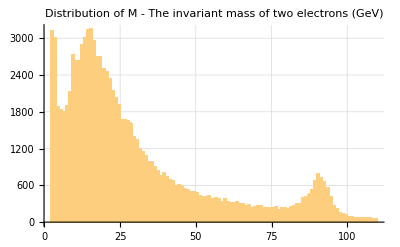
-Graphics-Frequency

```mathematica
Labeled[Histogram[filtercernd[[All,17]],100,GridLines->Automatic,ChartStyle->EdgeForm[None],PlotLabel->"Distribution of M - The invariant mass of two electrons (GeV)"],{Rotate["Frequency",90 Degree],""},{Left,Bottom}]
```

It has a concentration on the minimum value of 2 and two further peaks can be observed.

Numerical Features

Correlation matrix is the best way to observe the correlation between different coefficients of the data.

Plotting the correlation matrix of the dataset:

```mathematica
cor=Correlation[filtercernd[[All,1;;17]]];
plotlist=NumberForm[#,1]&/@(cor//Flatten);
collabels={"E1","px1","py1","pz1","pt1","eta1","phi1","Q1","E2","px2","py2","pz2","pt2","eta2","phi2","Q2","M"};
rowlabels=collabels;
rowticks=Thread[{Range[17],rowlabels}];
colticks=Thread[{Range[17],collabels}];
MatrixPlot[cor,Epilog->{Black,MapIndexed[Text[#1,#2-1/2]&,Transpose@Reverse@Partition[plotlist,17],{2}]},FrameTicks->{rowticks,colticks}]
```

-Graphics-

The parameters closely related are:

E1(2) and pt1(2)

phi1(2) and py1(2)

eta1(2) and pz1(2)

pt1(2) and M

Visualizing scatter plot of first three closely related set of parameters of both particles:

```mathematica
GraphicsGrid[{{Labeled[GraphicsRow[{ListPlot[filtercernd[[All,{1,5}]],Frame->True,FrameLabel->{"E1","pt1"},PlotLabel->"Corr coefficient - 0.7"],
ListPlot[filtercernd[[All,{9,13}]],Frame->True,FrameLabel->{"E2","pt2"},PlotLabel->"Corr coefficient - 0.6"]},ImageSize->Large],"Correlation between E and pt"]},{Labeled[GraphicsRow[{ListPlot[filtercernd[[All,{7,3}]],Frame->True,FrameLabel->{"ph1","py1"},PlotLabel->"Corr coefficient - 0.6",PlotStyle->Green],
ListPlot[filtercernd[[All,{15,11}]],Frame->True,FrameLabel->{"phi2","py2"},PlotLabel->"Corr coefficient - 0.6",PlotStyle->Green]},ImageSize->Large],"Correlation between phi and py"]},{Labeled[GraphicsRow[{ListPlot[filtercernd[[All,{6,4}]],Frame->True,FrameLabel->{"eta1","pz1"},PlotLabel->"Corr coefficient - 0.8",PlotStyle->Black],
ListPlot[filtercernd[[All,{14,12}]],Frame->True,FrameLabel->{"eta2","pz2"},PlotLabel->"Corr coefficient - 0.8",PlotStyle->Black]},ImageSize->Large],"Correlation between eta and pz"]}},ImageSize->600]
```

-Graphics-

All the scatter plots verify the strong correlations between different coefficients. One having highest coefficient can easily be correlated linearly under regression.

## Predicting the Invariant mass

In this section let’s use Mathematica’s machine learning functionalities and compare them for the task of predicting the invariant mass of electrons. First, we must reshape the data:

Shape the preprocessed data:

```mathematica
dataregression=Rule[#[[;;16]],#[[17]]]&/@filtercernd
```

{{58.7141,-7.31132,10.531,-57.2974,12.8202,-2.20267,2.17766,1,11.2836,-1.03234,-1.88066,-11.0778,2.14537,-2.34403,-2.07281,-1}→8.94841,{6.61188,-4.15213,-0.579855,-5.11278,4.19242,-1.02842,-3.00284,-1,17.1492,-11.7135,5.04474,11.4647,12.7536,0.808077,2.73492,1}→15.893,99996,{54.4622,11.3526,11.8809,51.924,16.4328,1.8678,0.808132,-1,8.58671,0.378009,3.07828,8.00705,3.10141,1.67717,1.44861,1}→4.6967,{7.64,0.886162,5.4789,-5.25033,5.5501,-0.842662,1.41044,1,52.1088,16.8075,-4.6051,49.1084,17.427,1.75925,-0.267427,-1}→36.5043}
 |  |  |  |

Split the data into a pair of shuffled training and testing sets using a Resource Function:

```mathematica
shuffledata=ResourceFunction["TrainTestSplit"][dataregression];
```

Define both the datasets:

```mathematica
{trainData,testData}=Through[{First,Last}[shuffledata] ];
```

Visualize a sample of dataset defined above:

```mathematica
RandomSample[testData, 5] // TableForm
```

{4.07276,-2.67017,2.70548,1.46216,3.80124,0.375748,2.34963,1,56.4124,6.74872,-6.72761,-55.6017,9.52922,-2.46426,-0.783832,-1}→26.3543
{37.1516,12.3483,-34.2448,7.41995,36.4031,0.202442,-1.22472,-1,109.215,-34.024,15.3238,102.642,37.3156,1.7365,2.71842,1}→92.0957
{24.6742,8.08142,10.3244,-20.9024,13.1112,-1.24593,0.906664,1,6.6082,-2.92386,4.54964,3.79739,5.40816,0.654434,2.14199,-1}→20.9324
{141.463,4.5268,64.252,125.949,64.4113,1.4235,1.50046,-1,28.59,4.01518,-8.38027,27.0377,9.29251,1.78947,-1.12399,1}→48.1528
{127.91,4.55045,20.7074,-126.141,21.2015,-2.48346,1.35448,1,41.8049,-6.97227,-17.8384,-37.1596,19.1525,-1.41656,-1.9434,-1}→46.0663

Train a PredictorFunction using ‘Nearest Neighbor’ method:

```mathematica
prNN=Predict[trainData,Method->"NearestNeighbors"]
```

PredictorFunction[…]

Visualize the information of the PredictorFunction:

```mathematica
Information[prNN]
```

Predictor information
Data type | Mixed (number: 16)
Standard deviation | 9.18 ± 0.4
Method | NearestNeighbors
Single evaluation time | 14.8 ms/example
Batch evaluation speed | 925. examples/s
Loss | 3.47 ± 0.032
Model memory | 12.7 MB
Training examples used | 80000 examples
Training time | 27.1 s
 |

Evaluate the performance of the PredictorFunction using the test data:

```mathematica
pmrNN=PredictorMeasurements[prNN,testData]
```

Predictor Measurements
Predictor method | NearestNeighbors
Number of test examples | 20000
Standard deviation | 7.39 ± 0.085
Standard deviation baseline | 25.2 ± 0.15
R-squared | 0.914 ± 0.0022
Mean cross entropy | 3.17 ± 0.013
Single evaluation time | 15.2 ms/example
Batch evaluation speed | 487. examples/s
-Graphics- |

Standard deviation is a measure of how dispersed the data is in relation to the mean. Low standard deviation means data are clustered around the mean, and high standard deviation indicates data are more spread out.  The predictor measurement information indicated we have a very diverse predicted dataset.

Train PredictorFunction using different methods:

```mathematica
Grid[{Information/@Map[Predict[trainData,Method->#]&,{"DecisionTree","LinearRegression","GradientBoostedTrees","RandomForest"}]}]
```

-Graphics-

Notice that Linear Regression took the most time to train and got the higher standard deviation while Random Forest took the less time and got the smaller standard deviation(despite GradientBoostedTrees method)

Create a custom neural network using NetChain:

```mathematica
cusnn=NetChain[{512,Ramp,256,Ramp,256,Ramp,128,Ramp,64,Ramp,32,Ramp,1}]
```

NetChain[…]

Train a custom neural network to predict the value of the invariant mass of electrons:

```mathematica
trainednn=NetTrain[cusnn,trainData,All,BatchSize->32,LearningRate->0.001]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:25000  rounds:10  time:5.0min  examples/s:2690
data | ,,  training examples:80000  processed examples:800000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:3.37
 | rounds
loss | -Graphics- | 
 | ]

Compare the resulting R^2 of the custom neural net with the Predict built - in function using the "NeuralNetwork" method:

```mathematica
<|"Custom Net"->NetMeasurements[trainednn["TrainedNet"],testData,"RSquared"],"Built-in Net"->PredictorMeasurements[Predict[trainData,Method->"NeuralNetwork"],testData,"RSquared"]|>
```

<|Custom Net→0.994487,Built-in Net→0.996298|>

R-squared is a goodness-of-fit measure for regression models. R-squared measures the strength of the relationship between a model and the dependent variable on a convenient 0 – 1 scale with 1 representing a model that explains all the variation in the response variable around its mean.
The R-squared value of both Custom and Built-in Net are very close to 1 and this proves the Neural Network we trained and chosen(methods) in this project very accurately predict the Invariant mass of the dielectron.

## Concluding remarks

We wanted to understand how a collision in high energy looks like. We chose collision of particles from Lepton family (in this project, electron.) We saw how Standard Model can be used to determine the basic features of the collision. We tried to understand the concept of ‘Invariant mass’ using different parameters of the collision. In  our project we are trying to predict the ‘Invariant mass’ instead of just taking Mean of the Invariant mass dataset or calculating through the formula. The project carries out as follows:
1. The dataset has been imported and preprocessed. 
2. Various features of the dataset have been analyzed randomly. Both particles had amazingly equal distribution of charges. 
3. We analyzed the closeness between different parameters using correlation matrix and  ‘scatter plotting’ them.
4.  We then shaped the dataset and divided them for training and testing.
5. We deployed different methods for the PredictorFunction on the training dataset.
6. We then created a custom Neural Network using NetTrain and trained it to predict Invariant mass.
We checked for the R-squared value of the dataset trained by the ‘custom’ and ‘built-in’ Neural Network and Voilà it fits perfectly.
 Particle physicists are constantly looking for more accurate tools for analyzing the collision and Machine Learning using Neural Network can be an optimum choice if it works perfectly in different processes like in our project.

### Future Plans and Ideas

My future plans involves further use of  databases generated by other type of decays like proton-proton(pp), hadronic collision, etc. This method can also be deployed even for complex decay processes and calculating different parameters of the collision. The idea can also be extended to collision types other than 2 -> 2.

## Keywords

Collision

LHC

Invariant mass

Machine learning

Particle physics

Neural Network

Electron

Data analysis

## Acknowledgment

Mentor: Julián Laverde

Thanks to my mentor Julián Laverde for his immense help in the project and Mike for brainstorming in sorting out the physics part. 
A big thanks to Rahul and other TA’s for bearing my stupid questions and codes.
Tuseeta and Mads for guiding throughout with their progress checks.
Last but not the least the fellow students of the School from whom I learned a lot.

## References

McCauley, Thomas; (2014). Events with two electrons from 2010. CERN Open Data Portal. DOI:10.7483/OPENDATA.CMS.PCSW.AHVG

Peskin, Michael E. THEORY OF e+ e- COLLISIONS AT VERY HIGH-ENERGY. Conf. Proc. C, 1987

PhysRevLett .86.1156. Search for Large Extra Dimensions in Dielectron and Diphoton Production. Phys. Rev. Lett, 2001

Arnison:163857. Experimental observation of lepton pairs of invariant mass around $95 GeV/c^2$ at the CERN SPS collider. Phys. Lett. B, 1985

T McCauley 2017 J. Phys.: Conf. Ser. 898 072030

arXiv:1604.02651v1 [nucl-ex] 10 Apr 2016

https://resources.wolframcloud.com/FunctionRepository/resources/StatisticsSummary

https://resources.wolframcloud.com/FunctionRepository/resources/TrainTestSplit

https://research.fit.edu/media/site-specific/researchfitedu/hep/heplaba/documents/research/CMS-JINST.pdf